```mathematica
data = {{36, 192}, {28, 113}, {28, 88}, {41, 294}, {19, 28}, {32, 123}, {22, 51}, {38, 252}, {25, 56}, {17, 16}, {31, 141}, {20, 32}, {25, 86}, {19, 21}, {39, 231}, {33, 187}, {17, 22}, {37, 205}, {23, 57}, {39, 265}}
```

{{36,192},{28,113},{28,88},{41,294},{19,28},{32,123},{22,51},{38,252},{25,56},{17,16},{31,141},{20,32},{25,86},{19,21},{39,231},{33,187},{17,22},{37,205},{23,57},{39,265}}

-191.124+11.0413 x

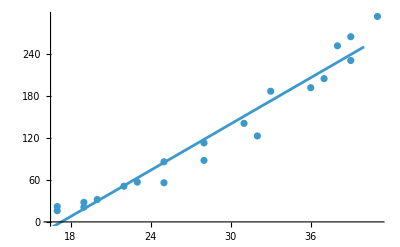

```mathematica
dataPlot := ListPlot[data]
fitLine = Fit[data, {x, 1}, x]
fitLinePlot := Plot[fitLine, {x, 0, 40}]
Show[dataPlot, fitLinePlot]
```

-4.85612+0.530958 x

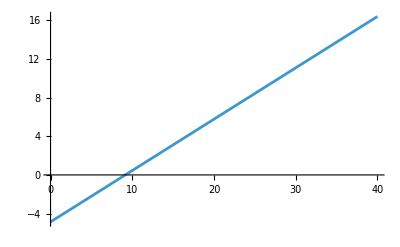

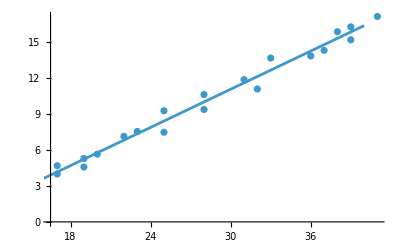

```mathematica
sqrtData := Table[{data[[i, 1]], Sqrt[data[[i, 2]]]}, {i, 1, Length[data]}]
sqrtPlot := ListPlot[sqrtData]
sqrtLine = Fit[sqrtData, {x, 1}, x] 
sqrtLinePlot = Plot[sqrtLine, {x, 0, 40}]
Show[sqrtPlot, sqrtLinePlot]
```

(-4.85612+0.530958 x)^2

{{36,203.301},{28,100.214},{28,100.214},{41,286.055},{19,27.3747},{32,147.247},{22,46.5801},{38,234.711},{25,70.86},{17,17.3903},{31,134.643},{20,33.2127},{25,70.86},{19,27.3747},{39,251.262},{33,160.415},{17,17.3903},{37,218.725},{23,54.1096},{39,251.262}}

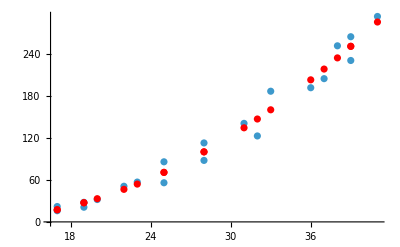

```mathematica
f[x_] = (-4.856124372382375+0.5309584367368706x)^2
predicted = Table[{data[[i, 1]], f[data[[i, 1]]]}, {i, 1, Length[data]}]
predPlot := ListPlot[predicted, PlotStyle->Red]
Show[dataPlot, predPlot]
```

4.2 question 4

```mathematica
data2= {{17, 19}, {19, 25}, {20, 32}, {22, 51}, {23, 57}, {25, 71}, {31, 141}, {32, 123}, {33, 187}, {36, 192}, {37, 205}, {38, 252}, {39, 248}, {41, 294}}
```

{{17,19},{19,25},{20,32},{22,51},{23,57},{25,71},{31,141},{32,123},{33,187},{36,192},{37,205},{38,252},{39,248},{41,294}}

8.58658×10^8-3.73579×10^8 x+7.2713×10^7 x^2-8.30745×10^6 x^3+611867. x^4-29737.4 x^5+908.204 x^6-12.8625 x^7-0.206398 x^8+0.0152992 x^9-0.000378713 x^10+5.21283×10^-6 x^11-3.96786×10^-8 x^12+1.31092×10^-10 x^13

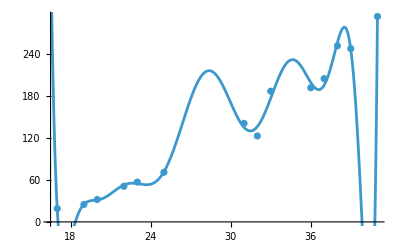

```mathematica
data2Plot := ListPlot[data2]
polyFit = Fit[data2, {1, x, x^2, x^3, x^4, x^5, x^6, x^7, x^8, x^9, x^10, x^11, x^12, x^13 }, x]
polyPlot := Plot[polyFit, {x, 0, 41}]
Show[data2Plot, polyPlot]
```

4.3 question 7

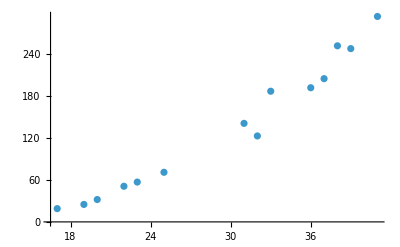

```mathematica
Show[data2Plot]
```

Making a divided difference table indicates this could be a quadratic function

37.6776-6.20192 x+0.300689 x^2

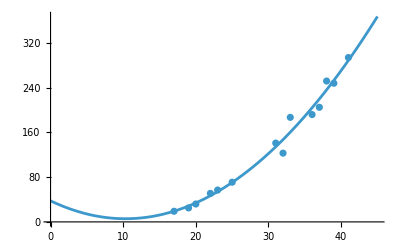

```mathematica
fitQuad = Fit[data2, {x^2, x, 1}, x]
fitQuadPlot := Plot[fitQuad, {x, 0, 45}]
Show[fitQuadPlot, data2Plot]
```